### a) Make a plot of the (h,r) plane

```mathematica
Solve[x*(r-x)+h == 0, x]
```

{{x→1/2 (r-√(4 h+r^2))},{x→1/2 (r+√(4 h+r^2))}}

```mathematica
Solve[D[x*(r-x)+h,x]==0,x]
```

{{x→r/2}}

```mathematica
x = r/2
```

r/2

```mathematica
Solve[x*(r-x)+h == 0,h]
```

{{h→-r^2/4}}

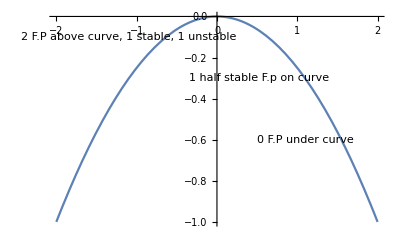

```mathematica
align[Right]={1,0};
align[Center]={0,0};        
align[Left]={-1,0};

lText=Text["0 F.P under curve",{0.5,-0.6},align[Left]];
cText=Text[" 2 F.P above curve, 1 stable, 1 unstable",{-1.1,-0.1},align[Center]];
rText=Text["1 half stable F.p on curve",{1.4,-0.3},align[Right]];

txt=Graphics[{lText,cText,rText}];
hc = Plot[-r^2/4,{r,-2,2}];

Show[hc,txt]
```

```mathematica
Clear[x]
```

### c) Find analytically the bifurcation curve[h_c(r),r]

```mathematica
derivative = D[h + x*r-x^2,x];
sol = Solve[derivative == 0,x]
```

{{x→r/2}}

```mathematica
x = r/2;
hc = Solve[x*(r-x)+h == 0,h];
hc
```

{{h→-r^2/4}}

```mathematica
(*From this we have hc, so the answer is just [-r^2/4,r]*)
```

#### b) Make the 3d plot of (x*,h,r) where f(x*,h, r) = 0

```mathematica
Solve[x*(r-x)+h == 0,r]
```

{{r→(-h+x^2)/x}}

```mathematica
Plot3D[(x^2-h)/x, {x,-4,4},{h,-4,4}]
```

-Graphics3D-

## d) find the transcritical bifurcation direction that depends on r

Start by taking the derivative of [h_c(r), r] and then normalize it

```mathematica
v1 = {-r^2/4, r}
v2 = D[v1,r]
```

{-r^2/4,r}

{-r/2,1}

```mathematica
Normalize[v2]
```

{-r/(2 √(1+Abs[r]^2/4)),1/(√(1+Abs[r]^2/4))}